```mathematica
dataGoogl=FinancialData["AMZN","Close",{{2013,12,31},{2020,7,20},"Daily"}];
```

```mathematica
stocksGoogl = QuantityMagnitude[dataGoogl]
```

TimeSeries[…]

```mathematica
trainSet = TimeSeriesWindow[stocksGoogl, {{2013, 12, 31},{2019, 3, 15}}];
testSet = TimeSeriesWindow[stocksGoogl, {{2019, 3, 18},{2020, 7, 2}}];
```

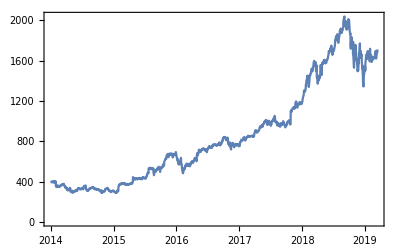

```mathematica
DateListPlot[trainSet]
```

```mathematica
Clear[a,b,c];
proc=EstimatedProcess[trainSet["Values"],GeometricBrownianMotionProcess[a,b,c]]
```

GeometricBrownianMotionProcess[0.00130354,0.0194668,398.79]

```mathematica
paths=RandomFunction[GeometricBrownianMotionProcess[0.001303539922648453,0.019466799007122632,testSet["FirstValue"]],{1,testSet["PathLength"],1},200];
```

```mathematica
td=TemporalData[paths["ValueList"],{testSet["FirstDate"],testSet["LastDate"]},ValueDimensions->1]
```

```mathematica
TemporalData[…]
```

TemporalData[…]

```mathematica
TimeSeriesForecast[proc, 1]
```

TimeSeriesForecast[GeometricBrownianMotionProcess[0.00130354,0.0194668,398.79],1]

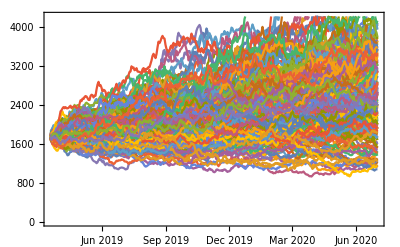

```mathematica
DateListPlot[td]
```

```mathematica
pp=DateListPlot[td,Joined->True]
```

-Graphics-

```mathematica
mF=TimeSeriesThread[Mean,td];
```

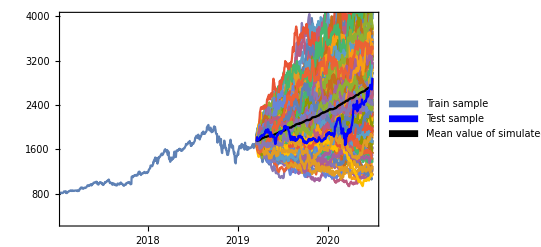
-Graphics-AMZN price

```mathematica
Labeled[Legended[Show[DateListPlot[trainSet,PlotRange->{{DateList[{"01/02/2017", {"Day", "Month", "Year"}}] ,td["LastTime"]},{Min[stocksGoogl],4000}},Joined->True],pp,DateListPlot[mF,Joined->True,PlotStyle->Directive[Thick,Black]], DateListPlot[testSet, Joined->True, PlotStyle->Directive[Thick,Blue]]],Placed[SwatchLegend[{RGBColor[0.368417, 0.506779, 0.709798],Blue,Black},{"Train sample","Test sample","Mean value of simulated paths"}],{.2,.8}]],"AMZN price"]
```

Доходность предсказанная:

```mathematica
mF["Values"][[-1]]/stocksGoogl["LastValue"] - 1
```

0.738675

```mathematica
stocksGoogl["LastValue"]
```

1823.28

```mathematica
mF["Values"][[-1]]
```

3170.09

```mathematica
2816.552430035657
```

2816.55

Предскажем остальные фин. активы:

```mathematica
data=FinancialData[{"MPC","FANG","UNH","EQIX","GOOGL"},"Close",{{2014,1,1},{2019,5,25},"Daily"}];
```

```mathematica
stocks= QuantityMagnitude[data]
```

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

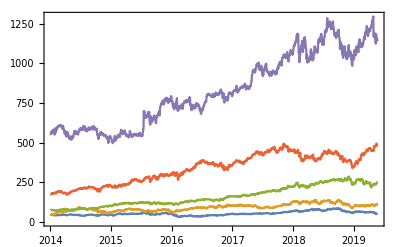

```mathematica
DateListPlot[stocks]
```

```mathematica
Clear[a,b,c];
proc2=EstimatedProcess[stocks[[#]]["Values"],GeometricBrownianMotionProcess[a,b,c]]&/@Range[1, 5]
```

{GeometricBrownianMotionProcess[0.000294287,0.0203954,44.74],GeometricBrownianMotionProcess[0.000825253,0.0243563,51.16],GeometricBrownianMotionProcess[0.000972771,0.0132416,74.57],GeometricBrownianMotionProcess[0.000869431,0.0140568,174.76],GeometricBrownianMotionProcess[0.000635756,0.0147105,557.089]}

```mathematica
paths2=RandomFunction[proc2[[#]],{stocks[[#]]["PathLength"],stocks[[#]]["PathLength"]+120,1},1000]&/@Range[1, 5];
```

```mathematica
td2=TemporalData[paths2[[#]]["ValueList"],{data[[#]]["LastDate"],Automatic},ValueDimensions->1]&/@Range[1, 5]
```

{TemporalData[…],TemporalData[…],TemporalData[…],TemporalData[…],TemporalData[…]}

Находим средние значения пересказанных доходностей:

```mathematica
mF2=TimeSeriesThread[Mean,td2[[#]]]&/@Range[1, 5];
```

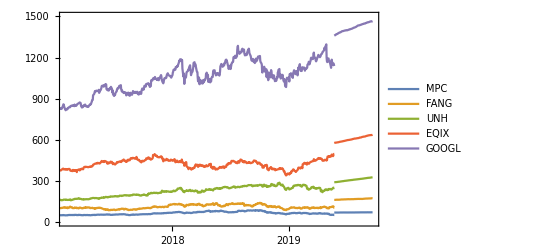

```mathematica
Show[DateListPlot[stocks ,td["LastTime"],Joined->True, PlotLegends->{"MPC","FANG","UNH","EQIX","GOOGL"}, PlotRange->{{DateList[{"01/02/2017", {"Day", "Month", "Year"}}] ,td2[[1]]["LastTime"]},{0,1500}}], DateListPlot[mF2,Joined->True,PlotStyle->Directive[Thick]]]
```

```mathematica
Export[ "stocks.png", %82]
```

stocks.png

```mathematica
SystemOpen["stocks.png"]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["stocks.png"]]]
```

Средние предсказанные доходности по акциям:
MPC:

```mathematica
mF2[[1]]["Values"][[-1]]/stocks[[1]]["LastValue"] - 1
```

0.396613

FANG:

```mathematica
mF2[[2]]["Values"][[-1]]/stocks[[2]]["LastValue"] - 1
```

0.589719

UNH:

```mathematica
mF2[[3]]["Values"][[-1]]/stocks[[3]]["LastValue"] - 1
```

0.30571

EQIX:

```mathematica
mF2[[4]]["Values"][[-1]]/stocks[[4]]["LastValue"] - 1
```

0.273853

GOOGL:

```mathematica
mF2[[5]]["Values"][[-1]]/stocks[[5]]["LastValue"] - 1
```

0.230699